```mathematica
β[r_]:=Piecewise[{{r^2+1,r≤1/2},{b,r>1/2}}]//PiecewiseExpand
u[r_]:=Piecewise[{{r^2,r≤1/2},{1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r]/b,r>1/2}}]//PiecewiseExpand
```

```mathematica
FL=D[β[r]u[r],r]//PiecewiseExpand
Limit[FL/.b->10^-3/.C->1/10,r->1/2]
Limit[FL/.b->10^3/.C->1/10,r->1/2]
```

Piecewise[{{Indeterminate, r==1/2}, {2 (r+2 r^3), r<1/2}, {(C+2 r^2+2 r^4)/r, True}}]

29/20

29/20

```mathematica
FL=D[u[r],r]//PiecewiseExpand
Limit[FL/.b->10^-3/.C->1/10,r->1/2]
Limit[FL/.b->10^3/.C->1/10,r->1/2]
```

Piecewise[{{Indeterminate, r==1/2}, {2 r, r<1/2}, {(C+2 r^2+2 r^4)/(b r), True}}]

1450

29/20000

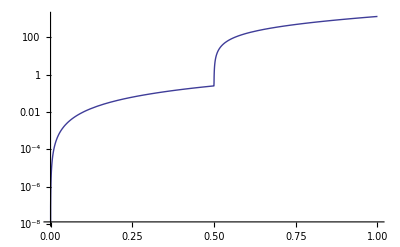

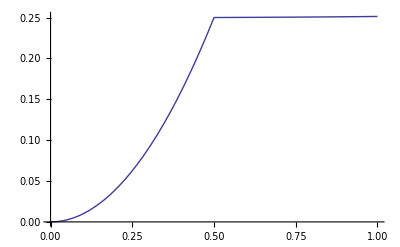

```mathematica
LogPlot[u[r]/.b->10^-3/.C->0.1,{r,0,1}]
Plot[u[r]/.b->10^3/.C->0.1,{r,0,1}]
```

```mathematica
2 r-(b C+2 r^2+2 r^4)/(b r)//Simplify
%/.r->1/2/.b->10^-3/.C->0.1
```

-C/r-(2 (r-b r+r^3))/b

-1249.2

```mathematica
2 (r+2 r^3)-(b C+2 r^2+2 r^4)/r//Simplify
%/.r->1/2/.b->10^-3/.C->0.1
```

-(b C)/r+2 r^3

0.2498

```mathematica
D[1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r]/b,r]
2r-%//Simplify
```

C/(b r)+(2 r+2 r^3)/b

-(C+2 r^2 (1-b+r^2))/(b r)